## Pendulum in Sphere

### Derivation

Rollbot is a sphere with a 1-DOF pendulum inside. The main body of the robot is a sphere with radius R, mass M, and moment of inertia of I in all directions. We can create a reference frame on the sphere’s solid body, with axes X’, Y’, and Z’. There’s a pendulum inside the body, which can be considered as a point of mass m hanging distance r away from the sphere’s center. The mass can only move on a circle which is parallel to the X’-Y’ plane and with center on Z’ axis, and the cone formed by the circle and the center of the sphere has a half tip angle of ϕ.

The state of the Rollbot is defined by 6 coordinates + 6 derivatives, 3 for sphere’s rotation, 2 for sphere’s center’s position (not counting Z), and 1 for pendulum’s position.

Let’s first consider a more general case where we have n point masses  that move on trajectories  specified in the body frame. The body frame O’-X’Y’Z’ is fixed to the sphere’s body and with center at the center of the sphere, and we have  where  are coordinates in a frame parallel to ground frame but with the origin O at the same spot as the center of sphere at this moment, coordinates in body frame, and transformation matrix from body frame to space frame respectively. We can first write down the motion of the point masses in the ground frame, , using their relative motion in the body frame , and then compile together an equation to determine the angular acceleration of the sphere using Newtonian dynamics. In future derivations,  is the coordinates of the center of the sphere, , are the components of angular velocity and acceleration of the sphere in ground frame respectively,  and  is the derivative of  w.r.t. time.





notice that the first part is only related to known quantities or less than 2rd order derivatives , and the second part is related to the second derivatives.

Now we can write down the Newton equation for all masses and the sphere:



and we have the rolling constraint

Take the constraint’s derivative, we have


Now we left multiply eqn2 with , sum with the third equation to get rid of supporting and friction force 

and then multiply the eqn1 with  and add with the previous equation to get rid of , we have:

We can now expand  using the aforementioned equation and then use constraint to replace all  with , and we have

Using equality  and name , we can further simplify this equation to

or


The physical meaning of this equation is clear. The first term is the negative of torque applied on the masses by the inertia and the gravity in the non-accelerating co-rotating frame with respect to the contact point of the sphere and the ground, and the second term is the moment of inertia matrix at this exact moment times the angular acceleration.

### Code

Draw the object

```mathematica
Clear["`*"]
circle3D[centre_:{0,0,0},radius_:1,normal_:{0,0,1},angle_:{0,2 Pi}]:=Composition[Line,Map[RotationTransform[{{0,0,1},normal},centre],#]&,Map[Append[#,Last@centre]&,#]&,Append[DeleteDuplicates[Most@#],Last@#]&,Level[#,{-2}]&,MeshPrimitives[#,1]&,DiscretizeRegion,If][First@Differences@angle>=2 Pi,Circle[Most@centre,radius],Circle[Most@centre,radius,angle]]

Object[{x_,y_},{α_,β_,γ_},t_]:=GeometricTransformation[{{Opacity@.3,Sphere[{0,0,0},R]},Black,Sphere[r1[t],0.05R],{Gray,Opacity@.3,circle3D[r{0,0,-Cos[ϕ]},r Sin[ϕ],{0,0,1}]},{Arrowheads[.03],Red,Arrow[Tube[{{0,0,0},{1,0,0}}0.4R,0.02R]],Green,Arrow[Tube[{{0,0,0},{0,1,0}}0.4R,0.02R]],Blue,Arrow[Tube[{{0,0,0},{0,0,1}}0.4R,0.02R]]}},TransformationFunction[ArrayFlatten@{{EulerMatrix[{α,β,γ}],{{x},{y},{R}}},{{{0,0,0}},{{1}}}}]]
```

Parameters

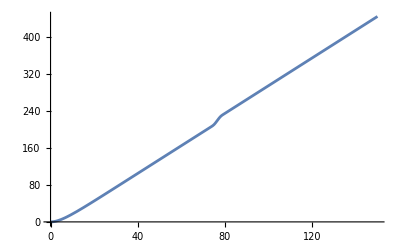

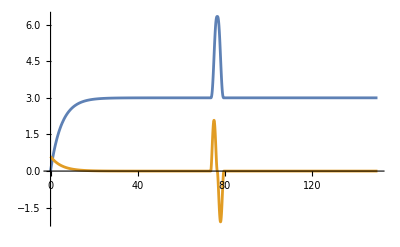

```mathematica
tmax=150;

ϕ=45Degree;
m=.306;
M=0.630+0.210+0.04;(*bottom + top + beads*)
r=.093;
R=.12;
II=2/3 0.56 0.119^2;
g=9.8;
kw=.4M R^2DiagonalMatrix[{1,1,1}];(*Friction coefficient*)

pulse[t_]:=UnitBox[t/2](1-3 t^2+3 t^4-t^6)
pulse[x0_,span_,t_]:=pulse[(t-x0)/span];
ramp[t_]:=Piecewise[{{1/2 (1+(15 t)/8-(5 t^3)/4+(3 t^5)/8),-1<t<1},{0,t<=-1},{1,t>=1}}]
ramp[x0_,span_,t_]:=ramp[(t-x0)/span]
rampv[t_]:=Evaluate@Integrate[ramp[t0],{t0,-1,t},Assumptions->(t>=-2)];
rampv[x0_,span_,t_]:=rampv[(t-x0)/span]

ClearAll[θ]
(*θθ[t_]:=3*5(t/5+Exp[-t/5]-1)+5(rampv[75.,1.6,t]-rampv[77,1.6,t])(*(pulse[29.,4.,t]-pulse[31.,4.,t])*);*)
θθ[t_]:=3*5(t/5+Exp[-t/5]-1)+5(rampv[75.,1.5,t]-rampv[78.0,1.5,t])(*(pulse[29.,4.,t]-pulse[31.,4.,t])*);
θ=Interpolation[{#,θθ[#]}&/@Range[0,tmax,0.05]];
Plot[θ[t],{t,0,tmax},PlotRange->Full]
Plot[{θ'[t],θ''[t]},{t,0,tmax},PlotRange->Full]
rθ[θ_]:=r{Cos[θ]Sin[ϕ],Sin[θ]Sin[ϕ],-Cos[ϕ]}
r1[t_]:=r{Cos[θ[t]]Sin[ϕ],Sin[θ[t]]Sin[ϕ],-Cos[ϕ]}
```

Solution and animation

```mathematica
ClearAll[α,β,γ,x,y];

T=EulerMatrix[{α[t],β[t],γ[t]}];
ω=FullSimplify[Extract[D[T,t].Inverse[T],{{3,2},{1,3},{2,1}}]];
ββ=FullSimplify[D[ω,t]];

Torque=((T.r1[t])×(m(D[{x[t],y[t],R}+T.r1[t],{t,2}]+{0,0,g}))).(T.{0,0,1});
TorquePower=Torque*θ'[t];

sol=NDSolve[{ββ==-Inverse[m(IdentityMatrix[3]({0,0,R}+T.r1[t]).({0,0,R}+T.r1[t])-Outer[Times,{0,0,R}+T.r1[t],{0,0,R}+T.r1[t]])+M R^2{{1,0,0},{0,1,0},{0,0,0}}+II IdentityMatrix[3]].(m({0,0,R}+T.r1[t])×(ω×(ω×(T.r1[t]))+2ω×(T.r1'[t])+T.r1''[t]+{0,0,g})+kw.ω),{α[0],β[0],γ[0]}=={0,ϕ,0},{α'[0],β'[0],γ'[0]}=={0,0,0},{x'[t],y'[t]}=={ω[[2]],-ω[[1]]}R,x[0]==y[0]==0},{α,β,γ,x,y},{t,0,tmax},Method->{"EquationSimplification"->"Residual","DiscontinuityProcessing"->False}][[1]]

pp=ParametricPlot[{x[t],y[t]}/.sol,{t,0,tmax},PlotStyle->Purple,ColorFunction->Function[{x,y,u},Hue[u]],Epilog->{Circle[R{-Tan[ϕ],0},R Tan[ϕ]]},PlotRange->Full]

{{xmin,xmax},{ymin,ymax}}=Options[pp,PlotRange][[1,2]];

Manipulate[Show[Graphics3D[{{Lighter[Blue,.8],InfinitePlane[{{0,0,0},{1,0,0},{0,1,0}}]},Opacity@.4,Object[{x[tt],y[tt]},{α[tt],β[tt],γ[tt]},tt]/.sol,Purple,Arrow[Tube[{{x[tt],y[tt],R},{x[tt],y[tt],R}+R Evaluate[ω/.t->tt]}/.sol]],Line[{{x[tt],y[tt],R},{x[tt],y[tt],0}}/.sol]},PlotRange->{{xmin-1.5R,xmax+1.5R},{ymin-1.5R,ymax+1.5R},{-0.1R,2.1R}},Lighting->"Neutral",Axes->True,AxesLabel->{"X","Y","Z"}],ParametricPlot3D[{x[t],y[t],0}/.sol,{t,0,Max[tt,0.01]},PlotPoints->1000,PlotStyle->Purple]],{{tt,tmax,"Time"},0,tmax},SaveDefinitions->True]
```

{α→InterpolatingFunction[…],β→InterpolatingFunction[…],γ→InterpolatingFunction[…],x→InterpolatingFunction[…],y→InterpolatingFunction[…]}

-Graphics-

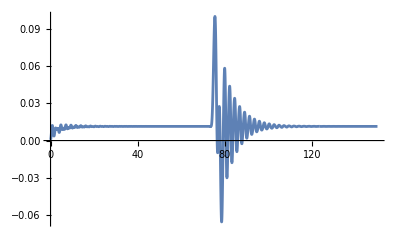

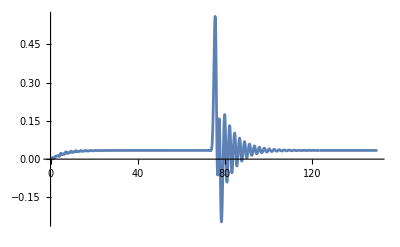

```mathematica
Plot[Evaluate[Torque/.sol],{t,0,tmax},PlotRange->Full,PlotPoints->200]
Plot[Evaluate[TorquePower/.sol],{t,0,tmax},PlotRange->Full,PlotPoints->200]
```

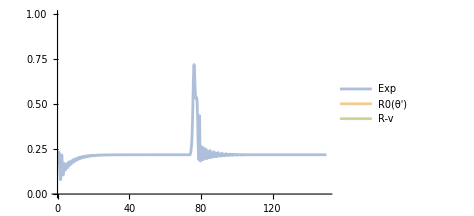

```mathematica
Plot[{(x'[t]^2+y'[t]^2)^(3/2)/Abs[y'[t]x''[t]-y''[t]x'[t]]/.sol,
Block[{rfunc=Interpolation[radiuslist[[;;,{1,2}]]]},rfunc[θ'[t]]],
Block[{Rvfunc=Interpolation@radiuslist[[;;,{6,2}]]},Rvfunc[Norm[{x'[t],y'[t]}/.sol]/R]]
},{t,0.5,tmax},PlotLegends->{"Exp","R0(θ')","R-v"},PlotStyle->Opacity@.5,PlotRange->{0,1}]
```

#### Static state analysis - approximate

Through simulations we can see that the Rollbot will rotate in a circle with fixed radius, and the radius seems to be R tan(ϕ) when angular velocity is low, and in such cases, the ball is hanging on the bottom, just slightly biased from z direction. This hints what the static state should look like:
-Graphics-
In the static state the whole sphere-mass assembly effectively rotate around a center point (the left corner of in the sketch), and the mass is tilted towards the center by angle δ and marginally to the front by distance z<<r (Notice that when we move the mass in direction perpendicular to the screen by z<<r, the mass will still be on the cone).
The motion of the sphere could be factored into two components:
	1) A self-spinning component to cancel out the rotation of the mass  which is aligned with Z’ direction (i.e. the cone’s symetrical axis).
	2) A orbiting component 

and the required torque to continue the static state can also be factored into two components:
	1) A component aligned with ω to cancel out the friction . 
	2) A component perpendicular to the screen to make it rotate along with the orbiting component.

Notice that component 1 can only be provided by the out-of-screen movement of the mass, and the vertical component is  pointing downwards, and the horizontal component is  pointing leftwards. To make it align with , we have , i.e. . As long as this could be satisfied, we could adjust z to compensate for the friction on ω.

We have:







Merge them together and we have:

```mathematica
radiuslist=With[{t0=Max[#,1.*^-3]},{t0,R ωx/Ω,δ,Ω,ωx,ωz,F,f/((m+M)g)}/.FindRoot[Evaluate@With[{R0=R ωx/Ω},{ωx==t0 Sin[δ+ϕ],-ωz+Ω==t0 Cos[δ+ϕ],-m Ω^2(R0-r Sin[δ]) ωx kw[[1,1]]==m g ωz kw[[3,3]],m g r Sin[δ]+(m Ω^2(R0-r Sin[δ]))r Cos[δ]-(m Ω^2(R0-r Sin[δ])+M Ω^2 R0) R==II ωx Ω}],{{δ,.7},{Ω,t0 Cos[ϕ]},{ωx,t0 Sin[ϕ]},{ωz,0}}]]&/@Range[0,10,.1];
```

Another possibility is when the cone is inverted and the mass is on the top.

```mathematica
radiuslist1=Quiet@With[{t0=#},{t0,R ωx/Ω,δ,Ω,ωx,ωz,F,f/((m+M)g)}/.FindRoot[Evaluate@With[{R0=R ωx/Ω},{ωx==t0 Sin[δ-ϕ],-ωz+Ω==t0 Cos[δ-ϕ],-m Ω^2(R0-r Sin[δ]) ωx kw[[1,1]]==m g ωz kw[[3,3]],m g r Sin[δ]+(m Ω^2(R0-r Sin[δ]))r Cos[δ]-(m Ω^2(R0-r Sin[δ])+M Ω^2 R0) R==II ωx Ω}],{{δ,Pi/2},{Ω,1},{ωx,t0 Sin[ϕ]},{ωz,0}}]]&/@Range[3.5,10,.1];
```

```mathematica
radiuslist2=Quiet@With[{t0=#},{t0,R ωx/Ω,δ,Ω,ωx,ωz,F,f/((m+M)g)}/.FindRoot[Evaluate@With[{R0=R ωx/Ω},{ωx==t0 Sin[δ-ϕ],-ωz+Ω==t0 Cos[δ-ϕ],-m Ω^2(R0-r Sin[δ]) ωx kw[[1,1]]==m g ωz kw[[3,3]],m g r Sin[δ]+(m Ω^2(R0-r Sin[δ]))r Cos[δ]-(m Ω^2(R0-r Sin[δ])+M Ω^2 R0) R==II ωx Ω}],{{δ,ϕ},{Ω,5},{ωx,1},{ωz,0}}]]&/@Range[3.5,10,.1];
```

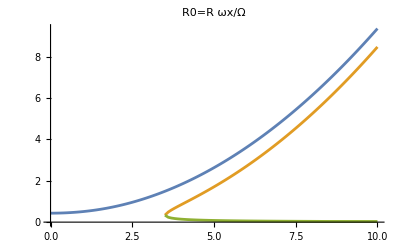
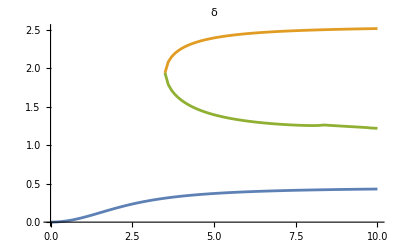
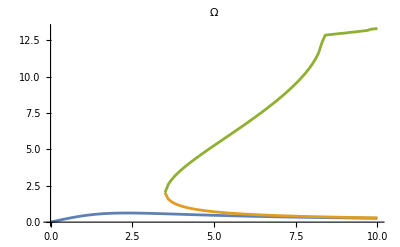
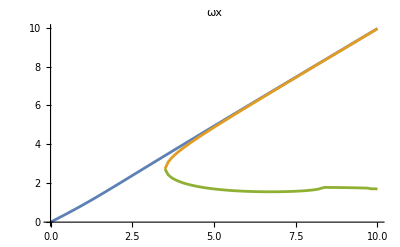
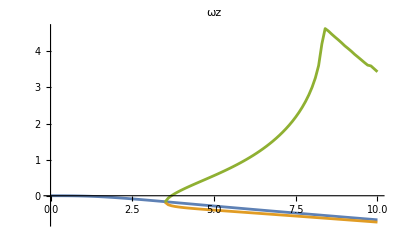

```mathematica
MapIndexed[ListLinePlot[{radiuslist[[;;,{1,#2[[1]]+1}]],radiuslist1[[;;,{1,#2[[1]]+1}]],radiuslist2[[;;,{1,#2[[1]]+1}]]},PlotLabel->#,PlotRange->Full]&,{"R0=R ωx/Ω","δ","Ω","ωx","ωz"}]
```

This is the plot used to determine whether the second solution exists.

```mathematica
Manipulate[Show@MapThread[Plot3D[#1,{Ω,-20,20},{δ,0,Pi},MeshFunctions->{#3&},Mesh->{{0}},MeshStyle->{#2},PlotStyle->Directive[Opacity@.3,#2],PlotPoints->50,AxesLabel->{"Ω","δ"}]&,{With[{R0=R t0 Sin[δ-ϕ]/Ω},{-m Ω^2(R0-r Sin[δ]) t0 Sin[δ-ϕ] kw[[1,1]]-m g (Ω-t0 Cos[δ-ϕ]) kw[[3,3]],m g r Sin[δ]+(m Ω^2(R0-r Sin[δ]))r Cos[δ]-(m Ω^2(R0-r Sin[δ])+M Ω^2 R0) R-II t0 Sin[δ-ϕ] Ω}],{Orange,Blue}}],{t0,0,10}]
```

Directly obtained from simulation

```mathematica
radiuslistexp=Monitor[Table[Block[{tmax=300,θ,r1,sol},
θ[t_]:=w0 10(t/10+Exp[-t/10]-1);
r1[t_]:=r{Cos[θ[t]]Sin[ϕ],Sin[θ[t]]Sin[ϕ],-Cos[ϕ]};

sol=NDSolve[{ββ==-Inverse[m(IdentityMatrix[3]({0,0,R}+T.r1[t]).({0,0,R}+T.r1[t])-Outer[Times,{0,0,R}+T.r1[t],{0,0,R}+T.r1[t]])+M R^2{{1,0,0},{0,1,0},{0,0,0}}+II IdentityMatrix[3]].(m({0,0,R}+T.r1[t])×(ω×(ω×(T.r1[t]))+2ω×(T.r1'[t])+T.r1''[t]+{0,0,g})+kw.ω),{α[0],β[0],γ[0]}=={0,ϕ,0},{α'[0],β'[0],γ'[0]}=={0,0,0},{x'[t],y'[t]}=={ω[[2]],-ω[[1]]}R,x[0]==y[0]==0},{α,β,γ,x,y},{t,0,tmax},Method->{"EquationSimplification"->"Residual","DiscontinuityProcessing"->False}][[1]];
{w0,With[{t=tmax},(x'[t]^2+y'[t]^2)^(3/2)/Abs[y'[t]x''[t]-y''[t]x'[t]]/.sol]}],{w0,.2,10,.1}],w0];
```

Stored results for ϕ = 60 Degree; m = .15; M = .5; r = .2; R = .25; II = 2/5 M R^2; g = 9.8; kw = .4 DiagonalMatrix[{.1, .1, .1}];

```mathematica
radiuslistexp=;
```

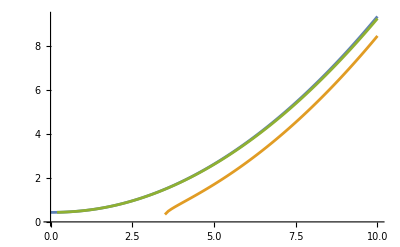

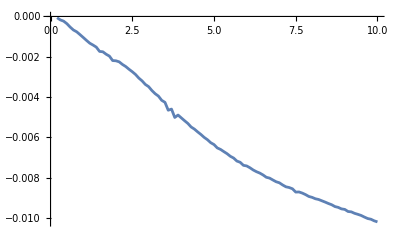

```mathematica
ListLinePlot[{radiuslist[[;;,{1,2}]],radiuslist1[[;;,{1,2}]],radiuslistexp},PlotRange->Full]
ListLinePlot[MapThread[{#1[[1]],(#2[[2]]-#1[[2]])/#2[[2]]}&,{radiuslist[[3;;,{1,2}]],radiuslistexp}],PlotRange->Full]
```

#### Static state analysis - precise

This is probably unnecessary as the approximate solution is already good enough. But on the other hand, this is not more complicated anyways.
In this analysis, we use δ as the angle of tilt of the symmetrical axis, and the mass is rotated by α from the bottom position.

```mathematica
radiuslist=Quiet@Table[With[{t0=Max[ω0,1.*^-3]},{t0,R t0 Sin[ξ]/Ω,θ0,ξ,Ω,t0 Sin[ξ],t0 Cos[ξ]-Ω}/.FindRoot[Evaluate@With[{R0=R t0 Sin[ξ]/Ω,kxy=kw[[1,1]],kz=kw[[3,3]],u={0,0,R}+EulerMatrix[{0,ξ,θ0}].{r Sin[ϕ],0,-r Cos[ϕ]}},{0,0,0}=={0,M Ω^2 R0 R,0}+m u×({0,0,-g}+Ω^2(u-u.{0,0,1} {0,0,1}+{R0,0,0}))+II Ω t0 Sin[ξ]{0,1,0}+kxy {t0 Sin[ξ],0,t0 Cos[ξ]-Ω}],{{ξ,ϕ},{Ω,t0 Cos[ϕ]},{θ0,0}}]],{ω0,0,10,.1}];
```

```mathematica
radiuslistanti=Table[With[{t0=Max[ω0,1.*^-3]},{t0,R t0 Sin[ξ]/Ω,θ0,ξ,Ω,t0 Sin[ξ],t0 Cos[ξ]-Ω}/.FindRoot[Evaluate@With[{R0=R t0 Sin[ξ]/Ω,kxy=kw[[1,1]],kz=kw[[3,3]],u={0,0,R}+EulerMatrix[{0,ξ,θ0}].{r Sin[ϕ],0,-r Cos[ϕ]}},{0,0,0}=={0,M Ω^2 R0 R,0}+m u×({0,0,-g}+Ω^2(u-u.{0,0,1} {0,0,1}+{R0,0,0}))+II Ω t0 Sin[ξ]{0,1,0}+kxy {t0 Sin[ξ],0,t0 Cos[ξ]-Ω}],{{ξ,Pi},{Ω,-4},{θ0,Pi}}]],{ω0,0,10,.1}];
```

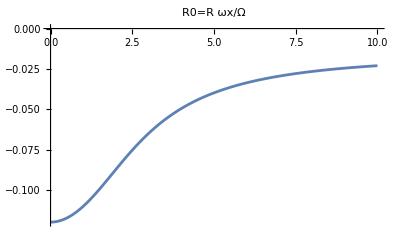
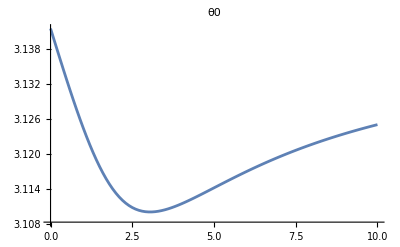
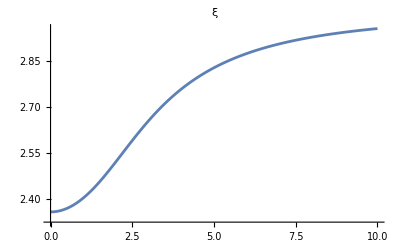
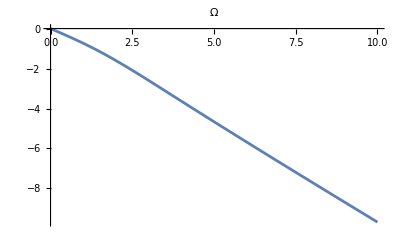
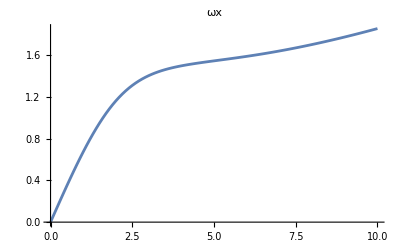
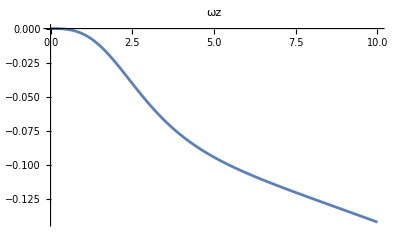

```mathematica
MapIndexed[ListLinePlot[radiuslist[[;;,{1,#2[[1]]+1}]],PlotLabel->#]&,{"R0=R ωx/Ω","θ0","ξ","Ω","ωx","ωz"}]
```

Different friciton coefficients

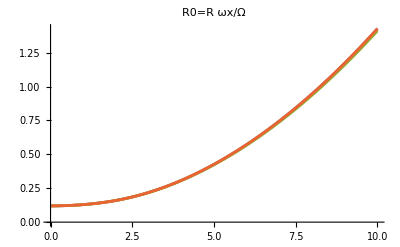
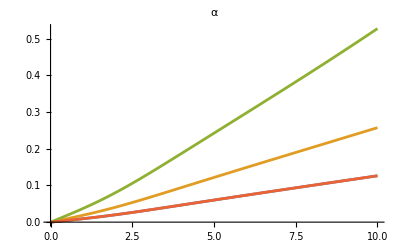
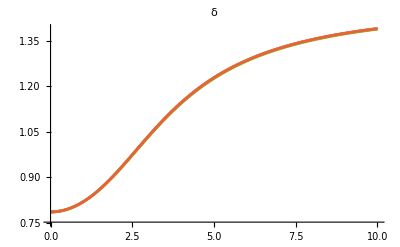
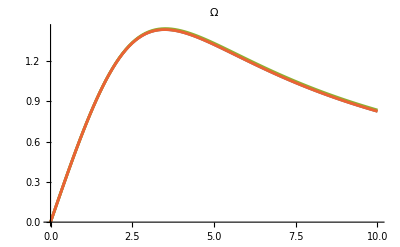
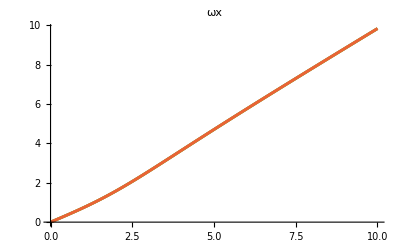
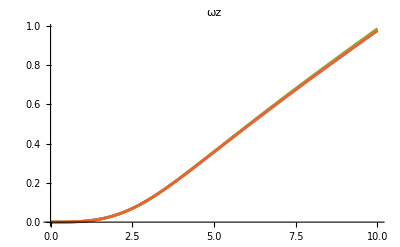

```mathematica
MapIndexed[ListLinePlot[{radiuslist[[;;,{1,#2[[1]]+1}]],radiuslist1[[;;,{1,#2[[1]]+1}]],radiuslist2[[;;,{1,#2[[1]]+1}]],
radiuslist3[[;;,{1,#2[[1]]+1}]]},PlotLabel->#]&,{"R0=R ωx/Ω","α","δ","Ω","ωx","ωz"}]
```

```mathematica
With[{t0=Max[3Pi,1.*^-3]},{t0,R t0 Sin[ξ]/Ω,θ0,ξ,Ω,t0 Sin[ξ],t0 Cos[ξ]-Ω}/.FindRoot[Evaluate@With[{R0=R t0 Sin[ξ]/Ω,kxy=kw[[1,1]],kz=kw[[3,3]],u={0,0,R}+EulerMatrix[{0,ξ,θ0}].{r Sin[ϕ],0,-r Cos[ϕ]}},{0,0,0}=={0,M Ω^2 R0 R,0}+m u×({0,0,-g}+Ω^2(u-u.{0,0,1} {0,0,1}+{R0,0,0}))+II Ω t0 Sin[ξ]{0,1,0}+kxy {t0 Sin[ξ],0,t0 Cos[ξ]-Ω}],{{ξ,ϕ},{Ω,t0 Cos[ϕ]},{θ0,0}}]]
```

{3 π,1.27535,0.241974,1.38068,0.870816,9.25497,0.910178}

### Disturbance analysis

```mathematica
ClearAll[sol]
ω0=10;
sol=With[{t0=ω0},FindRoot[Evaluate@With[{R0=R t0 Sin[ξ]/Ω,kxy=kw[[1,1]],kz=kw[[3,3]],u={0,0,R}+EulerMatrix[{0,ξ,θ0}].{r Sin[ϕ],0,-r Cos[ϕ]}},{0,0,0}=={0,M Ω^2 R0 R,0}+m u×({0,0,-g}+Ω^2(u-u.{0,0,1} {0,0,1}+{R0,0,0}))+II Ω t0 Sin[ξ]{0,1,0}+kxy {t0 Sin[ξ],0,t0 Cos[ξ]-Ω}],{{ξ,ϕ},{Ω,t0 Cos[ϕ]},{θ0,0}}]]
```

{ξ→1.38954,Ω→0.826472,θ0→0.0850279}

```mathematica
Block[{r=EulerMatrix[{0,ξ,θ0}].{r Sin[ϕ],0,-r Cos[ϕ]}/.sol,u,Ω=Ω/.sol,ωs=ω0{-Sin[ξ],0,-Cos[ξ]}/.sol,Ωv={0,0,Ω}/.sol,s={R ω0 Sin[ξ]/Ω,0,0}/.sol,α={αx[t],αy[t],αz[t]},eqn,coefarray,coef0,coef1,coefmat},
Echo@r;
u={0,0,R}+r;
eqn=FullSimplify[m(α×r)×(Ωv×(Ωv×(u+s)))
+m u×(Ωv×(Ωv×(α×r))+2Ωv×(D[α,t]×r)+D[α,{t,2}]×r)
+(m u+M R{0,0,1})×((D[α,t]×ωs+D[α,{t,2}])×{0,0,R})
+II(D[α,t]×ωs+D[α,{t,2}])
+m g(α×r)×{0,0,1}
+kw[[1,1]](α×ωs+D[α,t])];
coefarray=Transpose[Coefficient[eqn,#]&/@D[α,{t,#}]]&/@{0,1,2};
Echo[MatrixForm/@coefarray];
coef0=Inverse[coefarray[[3]]].coefarray[[1]];
coef1=Inverse[coefarray[[3]]].coefarray[[2]];
coefmat=ArrayFlatten[{{0,IdentityMatrix[3]},{-coef0,-coef1}}];
Echo@MatrixForm@coefmat;
Eigensystem@coefmat
]
```

{-0.0528723,0.00558478,-0.0763042}

{(0.229524 | -0.00301687 | -0.159036
0.0014732 | 0.214319 | 4.74338×10^-18
0.0227775 | 0.0167986 | -0.0157829),(0.00170784 | -0.0335787 | 0.000123431
0.0335787 | 0.00170784 | -0.19126
-0.000154126 | 0.0505425 | 0.00372498),(0.0185526 | 0.0000903557 | 0.000706951
0.0000903557 | 0.0193984 | -0.0000746736
0.000706951 | -0.0000746736 | 0.00615173)}

(0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
-12.2841 | 0.327085 | 8.51189 | -0.0841486 | 2.13303 | -0.0363086
-0.0275463 | -11.061 | -0.0335383 | -1.73056 | -0.130552 | 9.85785
-2.29127 | -2.90257 | 1.58701 | 0.0137177 | -8.46269 | -0.481683)

{{-0.11937+9.90012 ⅈ,-0.11937-9.90012 ⅈ,-0.0537422+3.2884 ⅈ,-0.0537422-3.2884 ⅈ,-0.355014,0.00485492},{{-0.0246099+0.00104775 ⅈ,-0.000902405-0.0748422 ⅈ,0.0623618-0.0006172 ⅈ,-0.00743516-0.243766 ⅈ,0.741055+0. ⅈ,-0.00133378+0.617463 ⅈ},{-0.0246099-0.00104775 ⅈ,-0.000902405+0.0748422 ⅈ,0.0623618+0.0006172 ⅈ,-0.00743516+0.243766 ⅈ,0.741055+0. ⅈ,-0.00133378-0.617463 ⅈ},{-0.00468194-0.28648 ⅈ,0.00101511+0.00195397 ⅈ,-0.00110024-0.0502854 ⅈ,0.942314+0. ⅈ,-0.00648+0.00323307 ⅈ,0.165418-0.000915579 ⅈ},{-0.00468194+0.28648 ⅈ,0.00101511-0.00195397 ⅈ,-0.00110024+0.0502854 ⅈ,0.942314+0. ⅈ,-0.00648-0.00323307 ⅈ,0.165418+0.000915579 ⅈ},{-0.525832+0. ⅈ,0.211112+0. ⅈ,-0.752997+0. ⅈ,0.186678+0. ⅈ,-0.0749479+0. ⅈ,0.267325+0. ⅈ},{-0.569506+0. ⅈ,0.000786622+0. ⅈ,-0.821972+0. ⅈ,-0.00276491+0. ⅈ,3.81899×10^-6+0. ⅈ,-0.00399061+0. ⅈ}}}

Scan

```mathematica
eigs=Table[Block[{ω0=Max[ωorig,1.*^-4],sol,rv,u,Ω,ωs,Ωv,s,α,eqn,coefarray,coef0,coef1,coefmat},
sol=FindRoot[Evaluate@With[{R0=R ω0 Sin[ξ]/Ω,kxy=kw[[1,1]],kz=kw[[3,3]],uu={0,0,R}+EulerMatrix[{0,ξ,θ0}].{r Sin[ϕ],0,-r Cos[ϕ]}},{0,0,0}=={0,M Ω^2 R0 R,0}+m uu×({0,0,-g}+Ω^2(uu-uu.{0,0,1} {0,0,1}+{R0,0,0}))+II Ω ω0 Sin[ξ]{0,1,0}+kxy {ω0 Sin[ξ],0,ω0 Cos[ξ]-Ω}],{{ξ,ϕ},{Ω,ω0 Cos[ϕ]},{θ0,0}}];

rv=EulerMatrix[{0,ξ,θ0}].{r Sin[ϕ],0,-r Cos[ϕ]}/.sol;
Ω=Ω/.sol;
ωs=ω0{-Sin[ξ],0,-Cos[ξ]}/.sol;
Ωv={0,0,Ω}/.sol;
s={R ω0 Sin[ξ]/Ω,0,0}/.sol;
α={αx[t],αy[t],αz[t]};

u={0,0,R}+rv;
eqn=FullSimplify[m(α×rv)×(Ωv×(Ωv×(u+s)))
+m u×(Ωv×(Ωv×(α×rv))+2Ωv×(D[α,t]×rv)+D[α,{t,2}]×rv)
+(m u+M R{0,0,1})×((D[α,t]×ωs+D[α,{t,2}])×{0,0,R})
+II(D[α,t]×ωs+D[α,{t,2}])
+m g(α×rv)×{0,0,1}
+kw[[1,1]](α×ωs+D[α,t])];
coefarray=Transpose[Coefficient[eqn,#]&/@D[α,{t,#}]]&/@{0,1,2};
coef0=Inverse[coefarray[[3]]].coefarray[[1]];
coef1=Inverse[coefarray[[3]]].coefarray[[2]];
coefmat=ArrayFlatten[{{0,IdentityMatrix[3]},{-coef0,-coef1}}];
Eigenvalues@coefmat
],{ωorig,0,3Pi,Pi/40}];
```

```mathematica
eigs=;
```

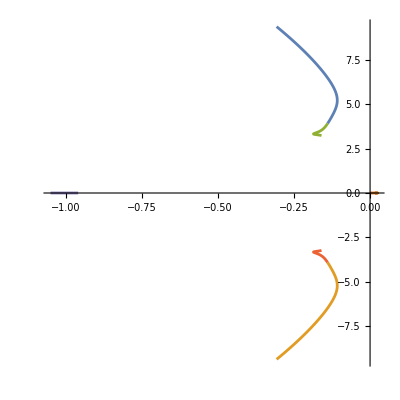

```mathematica
ComplexListPlot[Transpose@eigs,AspectRatio->1,PlotRange->Full,Joined->True]
```

#### Control Test

```mathematica
kw=.1(M+m)R^2DiagonalMatrix[{1,1,1}];
```

```mathematica
ClearAll[α,β,γ,x,y,θ];

T=EulerMatrix[{α[t],β[t],γ[t]}];
ω=FullSimplify[Extract[D[T,t].Inverse[T],{{3,2},{1,3},{2,1}}]];
ββ=FullSimplify[D[ω,t]];

Torque=((T.rθ[θ[t]])×(m(D[{x[t],y[t],R}+T.rθ[θ[t]],{t,2}]+{0,0,g}))).(T.{0,0,1});
TorquePower=Torque*θ'[t];

sol=NDSolve[{ββ==-Inverse[m(IdentityMatrix[3]({0,0,R}+T.rθ[θ[t]]).({0,0,R}+T.rθ[θ[t]])-Outer[Times,{0,0,R}+T.rθ[θ[t]],{0,0,R}+T.rθ[θ[t]]])+M R^2{{1,0,0},{0,1,0},{0,0,0}}+II IdentityMatrix[3]].(m({0,0,R}+T.rθ[θ[t]])×(ω×(ω×(T.rθ[θ[t]]))+2ω×(T.D[rθ[θ[t]],t])+T.D[rθ[θ[t]],{t,2}]+{0,0,g})+kw.ω),{α[0],β[0],γ[0]}=={0,ϕ,0},{α'[0],β'[0],γ'[0]}=={0,0,0},{x'[t],y'[t]}=={ω[[2]],-ω[[1]]}R,x[0]==y[0]==0,θ[0]==0,θ'[t]==4.5+0.5Cos[ArcTan[T[[1,3]],T[[2,3]]]]},{α,β,γ,x,y,θ},{t,0,tmax},Method->{"EquationSimplification"->"Residual","DiscontinuityProcessing"->False}][[1]]

pp=ParametricPlot[{x[t],y[t]}/.sol,{t,0,tmax},PlotStyle->Purple,ColorFunction->Function[{x,y,u},Hue[u]],Epilog->{Circle[R{-Tan[ϕ],0},R Tan[ϕ]]},PlotRange->Full]

{{xmin,xmax},{ymin,ymax}}=Options[pp,PlotRange][[1,2]];

Manipulate[Show[Graphics3D[{{Lighter[Blue,.8],InfinitePlane[{{0,0,0},{1,0,0},{0,1,0}}]},Opacity@.4,Object[{x[tt],y[tt]},{α[tt],β[tt],γ[tt]},tt]/.sol,Purple,Arrow[Tube[{{x[tt],y[tt],R},{x[tt],y[tt],R}+R Evaluate[ω/.t->tt]}/.sol]],Line[{{x[tt],y[tt],R},{x[tt],y[tt],0}}/.sol]},PlotRange->{{xmin-1.5R,xmax+1.5R},{ymin-1.5R,ymax+1.5R},{-0.1R,2.1R}},Lighting->"Neutral",Axes->True,AxesLabel->{"X","Y","Z"}],ParametricPlot3D[{x[t],y[t],0}/.sol,{t,0,Max[tt,0.01]},PlotPoints->1000,PlotStyle->Purple]],{{tt,tmax,"Time"},0,tmax},SaveDefinitions->True]
```

{α→InterpolatingFunction[…],β→InterpolatingFunction[…],γ→InterpolatingFunction[…],x→InterpolatingFunction[…],y→InterpolatingFunction[…],θ→InterpolatingFunction[…]}

-Graphics-

### Find Best Parameters

Reference case

```mathematica
ϕ=45Degree;
m=.30;
M=.6;
r=.09;
R=.12;
II=2/5(.45) R^2;
g=9.8;
kw=.2(M+m)R^2DiagonalMatrix[{1,1,1}];(*Friction coefficient*)
```

```mathematica
refradiuslist=;
```

Test case

```mathematica
ϕ=45Degree;
m=.256;
M=.19+0.355+0.206+.1;
r=.093;
R=.12;
II=2/3(.355+0.206) 0.118^2;
g=9.8;
kw=.1(M+m)R^2DiagonalMatrix[{1,1,1}];(*Friction coefficient*)

radiuslist=Table[With[{t0=Max[ω0,1.*^-3]},{t0/(2Pi),R ωx/Ω,α/Degree,δ/Degree,Ω/(2Pi),ωx/(2Pi),ωz/(2Pi)}/.FindRoot[Evaluate@With[{R0=R ωx/Ω,kxy=kw[[1,1]],kz=kw[[3,3]],rom=EulerMatrix[{0,δ,α}].{r Sin[ϕ],0,-r Cos[ϕ]}},{ωx==t0 Sin[δ],ωz+Ω==t0 Cos[δ],{-kxy ωx,-II Ω ωx,-kz ωz}==({0,0,R}×(m Ω^2ReplacePart[{R0,0,0}+rom,3->0]+{M Ω^2 R0,0,0})+rom×({0,0,-m g}+m Ω^2ReplacePart[{R0,0,0}+rom,3->0]))}],{{δ,ϕ},{Ω,t0 Cos[ϕ]},{ωx,t0 Sin[ϕ]},{ωz,0},{α,0}}]],{ω0,0,15,.1}];

MapIndexed[ListLinePlot[{Callout[radiuslist[[;;,{1,#2[[1]]+1}]],"this",Scaled@.6],Callout[refradiuslist[[;;,{1,#2[[1]]+1}]],"ref",Scaled@.4]},PlotLabel->#]&,{"R0=R ωx/Ω","α","δ","Ω","ωx","ωz"}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
test=Quiet@Table[With[{t0=Max[ω0,1.*^-5]},{ωx R,R ωx/Ω}/.FindRoot[Evaluate@With[{R0=R ωx/Ω,kxy=kw[[1,1]],kz=kw[[3,3]],rom=EulerMatrix[{0,δ,α}].{r Sin[ϕ],0,-r Cos[ϕ]}},{ωx==t0 Sin[δ],ωz+Ω==t0 Cos[δ],{-kxy ωx,-II Ω ωx,-kz ωz}==({0,0,R}×(m Ω^2ReplacePart[{R0,0,0}+rom,3->0]+{M Ω^2 R0,0,0})+rom×({0,0,-m g}+m Ω^2ReplacePart[{R0,0,0}+rom,3->0]))}],{{δ,ϕ},{Ω,t0 Cos[ϕ]},{ωx,t0 Sin[ϕ]},{ωz,0},{α,0}}]],{ω0,0,15,.01}];
```

```mathematica
fit=FindFit[test,d x^2+ee,{d,ee},x]
```

{d→0.781626,ee→0.125316}

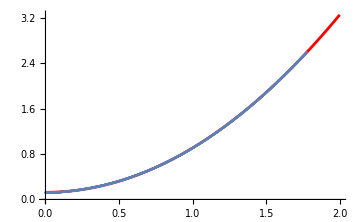

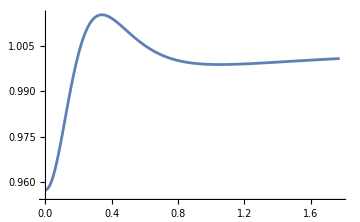

```mathematica
Show[Plot[d x^2+ee/.fit,{x,0,2},PlotStyle->Red],ListPlot[test]]
ListLinePlot[{#1,#2/(d #1^2+ee/.fit)}&@@@test,PlotRange->Full]
```

### LaTeX

```mathematica
<<MaTeX`
```

```mathematica
MaTeX["\\epsilon_{ijk}\\epsilon_{kmn}=\\delta_{im}\\delta_{jn}-\\delta_{in}\\delta_{jm}"]
```

-Graphics-

```mathematica
MaTeX["h(T,\\omega,r'(t))"]
```

-Graphics-

```mathematica
MaTeX["r_i=T_{ij}r'_j+s_i"]
```

-Graphics-

```mathematica
MaTeX["\\dot{r}_i=\\dot{T}_{ij}r_j'+T_{ij}\\dot{r}_j'+\\dot{s}_i=\\epsilon_{ijk}\\omega_j T_{kl}r_l'+T_{ij}\\dot{r}_j'+\\dot{s}_i"]
```

-Graphics-

```mathematica
MaTeX["\\ddot{r}_i=\\epsilon_{ijk}\\dot{\\omega}_j T_{kl}r_l'+\\epsilon_{ijk}\\omega_j \\dot{T}_{kl}r_l'+\\epsilon_{ijk}\\omega_j T_{kl}\\dot{r}_l'+\\dot{T}_{ij}\\dot{r}_j'+T_{ij}\\ddot{r}_j'+\\ddot{s}_i
=\\epsilon_{ijk}\\beta_j T_{kl}r_l'+\\epsilon_{ijk}\\omega_j \\epsilon_{kmn}\\omega_m T_{nl}r_l'+\\epsilon_{ijk}\\omega_j T_{kl}\\dot{r}_l'+\\epsilon_{ijk}\\omega_{j}T_{kl}\\dot{r}_l'+T_{ij}\\ddot{r}_j'+\\ddot{s}_i
=(\\epsilon_{ijk}\\omega_j \\epsilon_{kmn}\\omega_m T_{nl}r_l'+2\\epsilon_{ijk}\\omega_j T_{kl}\\dot{r}_l'+T_{ij}\\ddot{r}_j')+(\\ddot{s}_i+\\epsilon_{ijk}\\beta_j T_{kl}r_l')"]
```

-Graphics-

```mathematica
MaTeX["{}^q m{}^q \\ddot{r}_i={}^q F_i-{}^q m g\\hat{z}_i"]
```

-Graphics-

```mathematica
MaTeX["M \\ddot{s}_i=-\\sum_q {}^q F_i+N_i-Mg\\hat{z}_i"]
```

-Graphics-

```mathematica
MaTeX["I \\beta_i=-\\sum_q  \\epsilon_{ijk}{}^q r_j{}^q F_k+\\epsilon_{ijk}(-R\\hat{z}_j)N_k"]
```

-Graphics-

```mathematica
MaTeX["\\ddot{s}_i=\\epsilon_{ijk}\\beta_j(R\\hat{z}_k)"]
```

-Graphics-

```mathematica
MaTeX["\\epsilon_{ijk}(R\\hat{z}_j)"]
```

-Graphics-

```mathematica
-Graphics-
-Graphics-
```

```mathematica
MaTeX["\\epsilon_{ijk}(R\\hat{z}_j)M \\ddot{s}_k+I \\beta_i=-\\sum_q \\epsilon_{ijk}(R\\hat{z}_j+{}^q r_j){}^q F_k"]
```

-Graphics-

```mathematica
MaTeX["\\epsilon_{ijk}(R\\hat{z}_j+{}^q r_j)"]
```

-Graphics-

```mathematica
MaTeX["I \\beta_i=-\\sum_q  \\epsilon_{ijk}{}^q r_j{}^q F_k+\\epsilon_{ijk}(-R\\hat{z}_j)N_k"]
```

-Graphics-

```mathematica
MaTeX["\\sum_q\\epsilon_{ijk}(R\\hat{z}_j+{}^q r_j)({}^q m{}^q \\ddot{r}_k + {}^q m g\\hat{z}_k)+\\epsilon_{ijk}(R\\hat{z}_j)M \\ddot{s}_k+I \\beta_i=0"]
```

-Graphics-

```mathematica
MaTeX["\\sum_q{}^q m\\epsilon_{ijk}(R\\hat{z}_j+{}^q r_j)({}^q h_k+g\\hat{z}_k) +\\sum_q{}^q m\\epsilon_{ijk}\\epsilon_{kmn}(R\\hat{z}_j+{}^q r_j)\\beta_m(R\\hat{z}_n+{}^q r_n)+M\\epsilon_{ijk}\\epsilon_{kmn}(R\\hat{z}_j)\\beta_m(R\\hat{z}_n)+I \\beta_i=0"]
```

-Graphics-

```mathematica
MaTeX["\\sum_q{}^q m\\epsilon_{ijk}{}^q u_j({}^q h_k+g\\hat{z}_k) +\\sum_q{}^q m(\\beta_i{}^q u_j{}^q u_j-\\beta_j{}^q u_j{}^q u_i)+M( \\beta_i(R\\hat{z}_j)(R\\hat{z}_j)-\\beta_j(R\\hat{z}_j) (R\\hat{z}_i))+I \\beta_i=0"]
```

-Graphics-

```mathematica
MaTeX["\\sum_q{}^q m\\epsilon_{ijk}{}^q u_j({}^q h_k+g\\hat{z}_k) +\\beta_i\\left(\\sum_q{}^q m(\\delta_{ik}{}^q u_j{}^q u_j-{}^q u_i{}^q u_k)+M(\\delta_{ik}(R\\hat{z}_j)(R\\hat{z}_j)-(R\\hat{z}_i) (R\\hat{z}_k))+I\\right)=0"]
```

-Graphics-

```mathematica
MaTeX["{}^q u_i=R\\hat{z}_i+{}^q r_i"]
```

-Graphics-

```mathematica
MaTeX["\\epsilon_{ijk}\\epsilon_{kmn}=\\delta_{im}\\delta_{jn}-\\delta_{in}\\delta_{jm}"]
```

-Graphics-

```mathematica
MaTeX["dR/ds=dR/dt*dt/ds=dR(\\dot{\\theta})/d\\dot{\\theta}*d\\dot{\\theta}/dt*1/v(\\dot{\\theta})\\leq(dR(\\dot{\\theta})/d\\dot{\\theta})/v(\\dot{\\theta})*\\beta_{max}"]
```

-Graphics-

```mathematica
MaTeX["v(R)*(d\\dot{\\theta}(R)/dR)*dR/ds\\leq\\beta_{max}"]
```

-Graphics-

```mathematica
MaTeX["v(R)*(d\\dot{\\theta}(R)/dR)"]
```

-Graphics-